```mathematica
(* This code takes long-term-array (.lta) data from the wavemeter and finds the
transition points. Then it isolates these transition points so that an array
is obtained that roughly corresponds to the sequence of Detunings measured.
*)
dropBoxOn=FileNameJoin[{"Dropbox","00School","research"}];
labComp=FileNameJoin[{"C:","Users","karl",dropBoxOn}];
homeComp=FileNameJoin[{"/","home","karl",dropBoxOn}];

(*Add on the specific folder that you're interested in.*)
dataFolder=FileNameJoin[{homeComp,"4-22-17"}]

(* Accessing files is simplified if we set our directory to where the files are located*)
SetDirectory[dataFolder];
(* The name of the datafile you wish to analyze *)
longTermDataFileName="posDetuningsSlow.lta"
fileNames=FileNames["*.lta"]
```

```mathematica
ltData=Import[fileNames[[1]],"tsv"];
(* Removes the standard header information that is contained in every long-term 
analysis datafile *)
headerDoneLine=47;
ltData=Take[ltData,{headerDoneLine,-1},{1,2}];

{timeMs,waveLength}=Transpose[ltData];

timeS=N[timeMs]/1000;
detuning=299792458/waveLength-377107.463;

ltDataAll=Dataset[Transpose[{timeS,detuning}]];
ListPlot[ltDataAll,PlotRange-> {Full,{-30,30}},GridLines->{Range[359.55,630,6.59],Range[-25,20,.5]}]
```

-Graphics-

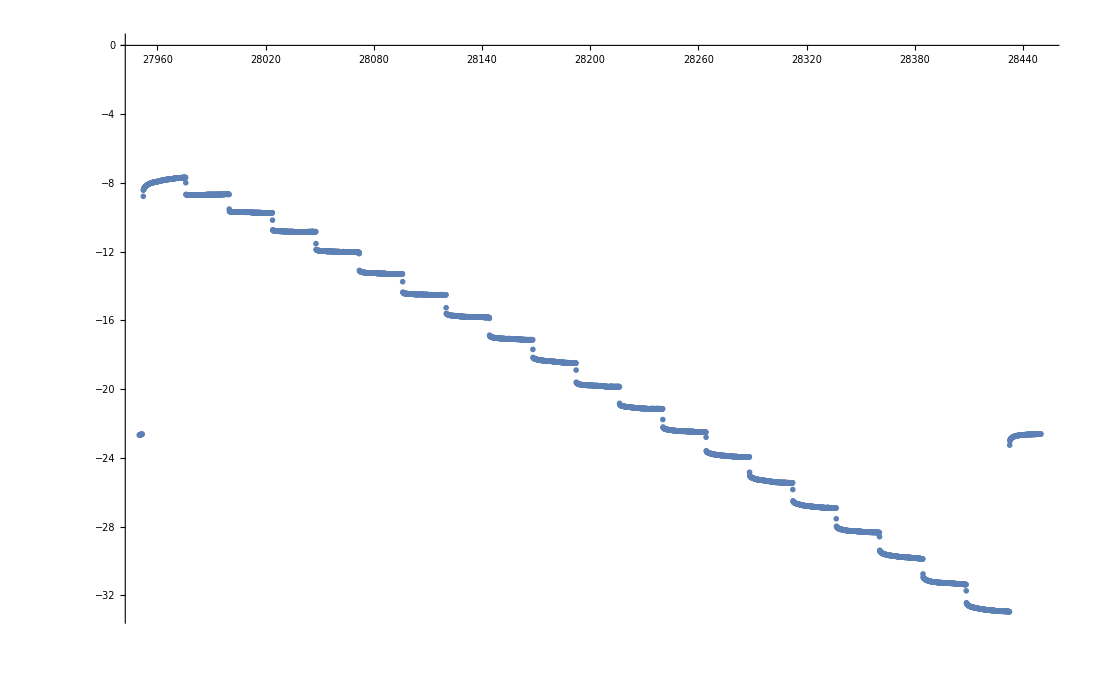

Dataset[<>]

```mathematica
(*These values of where the data starts and ends should be obtained
by inspecting the datapoints. *)
dataRunStart=26980+485*2;
dataRunEnds={27480+485*2};
dataStart=dataRunStart;
dataEnd=dataRunEnds[[1]];
timeBetweentransitions=20;
numberOfFrequencies=20;
transistionSize=
frequenciesList={};

For[i=1,i<=Length[dataRunEnds],i++,
dataEnd=dataRunEnds[[i]];
(*Removes the data at the beginning that we're not interested in *)
ltData=ltDataAll[Select[Abs[#[[1]]]>dataStart&]];
(* Ditto for the end *)
ltData=ltData[Select[Abs[#[[1]]]<dataEnd&]];
Print[ListPlot[ltData]];
dataStart=dataRunEnds[[i]];

(** Make the data into two lists. **)
{timeS,detuning}=Transpose[Normal[ltData]];

(* Calculate the difference in detuning between successive values, put this in a new matrix this is how we determine if a transition was made. A large value of detuningDiff indicates the laser quickly changed frequency. *)
detuningDiff=Table[ltData[[i]][[2]]-ltData[[i+1]][[2]],{i,1,Length[ltData]}];
(* The last difference isn't a pretty number. Set it to zero so Mathematica doesn't complain *)
detuningDiff[[-1]][[2]]=0;
newMatrix=Dataset[Transpose[{timeS,detuning,detuningDiff}]];

(* Remove all data points that aren't near a transition *)
transitionSpots=newMatrix[Select[Abs[#[[3]]]>.5&]];
{timeSTrans,detuningTrans,detuningDiff}=Transpose[Normal[transitionSpots]];

(* Calculate the time difference between the transitions. We know that our transitions
will happen at regular intervals, so make sure that the "transition spots" aren't too close together. *)
timeDiff=Table[transitionSpots[[i-1]][[1]]-transitionSpots[[i]][[1]],{i,1,Length[transitionSpots]}];
(* Again, stop mathematica from complaining *)
timeDiff[[1]][[2]]=0;
newMatrix=Dataset[Transpose[{timeSTrans,detuningTrans,detuningDiff,timeDiff}]];

(* Select out the data that are too close to each other to be a transition *)
transitionSpots=newMatrix[Select[Abs[#[[4]]]>timeBetweentransitions&]];
Print[transitionSpots];

alist=Normal[Take[transitionSpots,All,{2}]];
For[k=1,k<=Length[transitionSpots],
transitionPos=Position[timeS,transitionSpots[[k]][[1]]][[1]][[1]];
alist[[k]]=Mean[Take[detuning,{transitionPos-9,transitionPos-4}]];
k++;
];
AppendTo[frequenciesList,alist];
]
{nothing,nothing,nothing,timeBetweenArray}=Transpose[Normal[transitionSpots]]
frequenciesList
```

```mathematica
frequenciesListEdit=frequenciesList
valuesToRemoveFromStart=1;
valuesToRemoveFromEnd=0;
frequenciesListEdit[[1]]=Take[frequenciesList[[1]],{(1+valuesToRemoveFromStart),-(1+valuesToRemoveFromEnd)}];
(*frequenciesListEdit[[2]]=Take[frequenciesList[[2]],{3,-2}];*)
Length[frequenciesListEdit[[1]]]
(*Length[frequenciesListEdit[[2]]]*)
frequenciesListEdit
avgScanTime=Abs[Mean[Take[timeBetweenArray,{4,-2}]]]
```

{{-22.6477,-7.69148,-8.66151,-9.74458,-10.8435,-12.0404,-13.2958,-14.5156,-15.831,-17.1291,-18.4809,-19.8572,-21.1489,-22.503,-23.9394,-25.4524,-26.918,-28.3456,-29.8712,-31.3613,-32.9351}}

20

{{-7.69148,-8.66151,-9.74458,-10.8435,-12.0404,-13.2958,-14.5156,-15.831,-17.1291,-18.4809,-19.8572,-21.1489,-22.503,-23.9394,-25.4524,-26.918,-28.3456,-29.8712,-31.3613,-32.9351}}

24.0484

```mathematica
transitions=Range[numberOfFrequencies];
stdDev=Range[numberOfFrequencies];
transitionTime=avgScanTime;
transitionEnd=transitionSpots[[-(1+valuesToRemoveFromEnd),1]];
timeRange={transitionEnd-transitionTime,transitionEnd};
For[j=1,j≤numberOfFrequencies,j++,
shortList=ltDataAll[Select[Abs[#[[1]]]>timeRange[[1]]+.005&]];
shortList=shortList[Select[Abs[#[[1]]]<timeRange[[2]]-.005&]];
{time,detune}=Transpose[Normal[shortList]];

transitions[[-j]]=Mean[detune];
stdDev[[-j]]=StandardDeviation[detune];
timeRange=timeRange-transitionTime;
]
transitions
stdDev
```

{-7.88309,-8.67973,-9.71348,-10.8312,-11.9886,-13.2598,-14.4836,-15.7668,-17.0625,-18.3796,-19.791,-21.0864,-22.4282,-23.862,-25.3416,-26.8148,-28.2529,-29.7331,-31.2468,-32.8121}

{0.177806,0.0835867,0.0766215,0.0504737,0.0892687,0.0880777,0.0997266,0.103636,0.126598,0.123093,0.120453,0.102683,0.11595,0.107811,0.141591,0.114032,0.127433,0.128062,0.130988,0.134004}

```mathematica
ListPlot[ltDataAll,PlotRange-> {{transitionEnd-(numberOfFrequencies+1)*avgScanTime,transitionEnd},Automatic},GridLines->{Range[(transitionEnd-numberOfFrequencies*avgScanTime),transitionEnd,avgScanTime],Range[-25,20,.5]}]
```

-Graphics-

```mathematica
Export["032338.tsv",transitions]
```

032338.tsv

```mathematica
For[i=1,i<=Length[frequenciesListEdit],i++,
Export["RunNumber"<>ToString[i]<>".tsv",frequenciesListEdit[[i]]]
]
```

```mathematica
(* This second part of the code attempts to correct for "drifting effects" 
of the laser. Whenever the wavelength is changed, the frequency continues 
to drift for a period of time. If a long period of time is allowed so
that all of this drifting can occur, the following code takes the transition points
and looks at the frequency measured several miliseconds before the transition
was made. I found that in general, this results in corrections of ~.04 GHz, and was
therefore not a worthy pursuit. I keep the code here just in case I ever change my mind. 
*)

(*alist=Transpose[{alist}]*)
Export["secondRunDetunings.tsv",alist]
```

{{10.7692},{23.6873},{22.6673},{21.3959},{20.4613},{19.2847},{17.8378},{16.8842},{15.6318},{13.9904},{12.9799},{11.7038},{9.96279},{9.17056},{10.921}}

15

{23.5995,22.6546,21.5975,20.4731,19.3203,18.1248,16.9222,15.68,14.3786,13.0598,11.7536,10.4435,9.12708}

secondRunDetunings.tsv